# E1: Introduction to Circuits

Calvin Zikakis
TA: Drew Morrill
Section 311
February 15th 2017
Partner: Kristen Kyle

## Introduction

In this lab, we are going to explore different instrumentation used in electric circuits, including DC power supply, a digital multimeter (to measure resistance, current, and voltage), and an oscilloscope. We used these tools along with basic circuits to measure resistance and current of a light bulb filament and show the relationship between voltage, current, and resistance known as Ohm’s Law. We used precision tools such as the oscilloscope in order to measure the frequency of a signal with help from a photodiode. Finally, in part 3, we constructed our own circuits in order to measure resistance, current, and voltage analytically and experimentally. This lab shows importance because it familiarize us with the tools we will be using later in the class.

## Data and Calculations

```mathematica
Rsystem = 1.0; (*Bulb+Wire resistance in Ohms*) 
Rwires = 0.4; (*Resistance of the wires in Ohms*)
δR = 0.01; (*Uncertianty on the DMM in Ohms*)
Rbulb = Rsystem-Rwires (*Resistance of the bulb in Ohms*)
δRbulb = √(δR^2+δR^2)(*Uncertianty of the resistance in Ohms*)
```

0.6

0.0141421

### Table

```mathematica
Vbulb = {.05, .1, .15, .2, .25, .3, .35, .4, .5, .6, .7, .8, 1, 1.2, 1.4, 1.6, 1.9, 2.2, 2.5, 2.8}; (*Voltage across the bulb in Volts*)
Ibulb = {.045, .095, .126, .158, .188, .211, .23, .244, .27, .293, .309, .322, .34, .362, .38, .397, .424, .461, .499, .534} (*Current through the bulb in Amps*);
VvsI = Thread[{Ibulb, Vbulb}]

Rbulb = Vbulb/Ibulb; (*Resistance of the Bulb in Ohms*)
Pbulb = Ibulb*Vbulb ;(*Power of the bulb in Watts*)

BulbData = Thread[{Vbulb,Ibulb,Rbulb,Pbulb}];
NumberForm[Grid[Prepend[BulbData,{"Voltage (V)","Current (A)","Resistance (Ω)","Power (W)"}], Frame->All],{Infinity,3}]

RvsI = Thread[{Ibulb,Rbulb}];
PvsI = Thread[{Ibulb,Pbulb}];

ListPlot[VvsI,PlotLabel->"Plot of Voltage vs. Current",AxesLabel -> {"Current (A)","Voltage (V)"}]
ListPlot[RvsI,PlotLabel->"Plot of Resistance vs. Current",AxesLabel -> {"Current (A)","Resistance (Ω)"}]
ListPlot[PvsI,PlotLabel->"Plot of Power vs. Current",AxesLabel -> {"Current (A)","Power (W)"}]
```

{{0.045,0.05},{0.095,0.1},{0.126,0.15},{0.158,0.2},{0.188,0.25},{0.211,0.3},{0.23,0.35},{0.244,0.4},{0.27,0.5},{0.293,0.6},{0.309,0.7},{0.322,0.8},{0.34,1},{0.362,1.2},{0.38,1.4},{0.397,1.6},{0.424,1.9},{0.461,2.2},{0.499,2.5},{0.534,2.8}}

Voltge (V) | Current (A) | Resistance (Ω) | Power (W)
0.050 | 0.045 | 1.111 | 0.002
0.100 | 0.095 | 1.053 | 0.010
0.150 | 0.126 | 1.190 | 0.019
0.200 | 0.158 | 1.266 | 0.032
0.250 | 0.188 | 1.330 | 0.047
0.300 | 0.211 | 1.422 | 0.063
0.350 | 0.230 | 1.522 | 0.081
0.400 | 0.244 | 1.639 | 0.098
0.500 | 0.270 | 1.852 | 0.135
0.600 | 0.293 | 2.048 | 0.176
0.700 | 0.309 | 2.265 | 0.216
0.800 | 0.322 | 2.484 | 0.258
1.000 | 0.340 | 2.941 | 0.340
1.200 | 0.362 | 3.315 | 0.434
1.400 | 0.380 | 3.684 | 0.532
1.600 | 0.397 | 4.030 | 0.635
1.900 | 0.424 | 4.481 | 0.806
2.200 | 0.461 | 4.772 | 1.014
2.500 | 0.499 | 5.010 | 1.248
2.800 | 0.534 | 5.243 | 1.495

### Plots

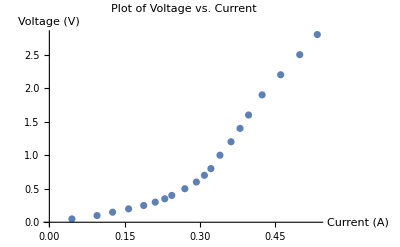

This plot shows the relationship between voltage and current of the light bulb filament. As voltages increases, current does as well.

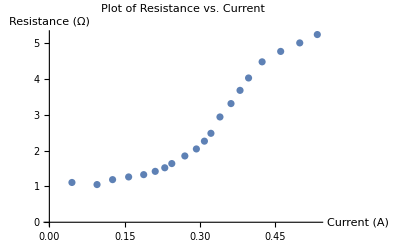

This plot shows how resistance changes as current changes in the light bulb filament. As current increases, the resistance does as well.

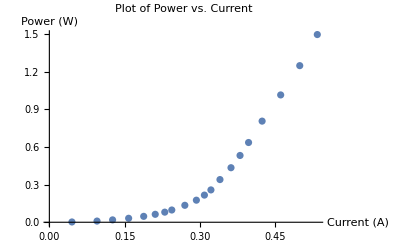

This plot shows the relationship between power and current. Reading the data we can easily see the quadratic shape of this graph showing an increase in current also results in an increase of power.

## Conclusion

In this lab we learned the relationship between current, voltage, resistance, and power. Our data showed us that as voltage increases, current will as well. It showed the relationship of resistance and current and how if one increases the other does as well. The lab also showed us how an increase in power results in an increase of current. In summary as current increases, everything else did as well. We explored the characteristics of a light bulb filament by measuring voltage, current, and calculation resistance. We saw how light bulb filament changes resistance based off of its temperature. Part 2 allowed us to become familiarized with the oscilloscope in order to measure the oscillation period of a light. In part 3 we learned about the effects resisters have on a circuit. Overall, this lab showed the relation between all of the section of Ohm’s Law.